```mathematica
(*
holo = %holo im Gleichgewicht
b= Kpre= [apoA]/[ApoB]
c= logKd
l= Anfangskonzentration von Adenine
r= Anfangskonzentration von RNA
*)
R=8.3144621 (*J/mol*K*)
DeltaHbind=110470.2357608338
DeltaSbind=238.303284932985
DeltaHpre=52002.80824997664
DeltaSpre=167.28088132812806
(*Daten sind aus Kd_und_Kpre_function_of_T.nb the values for Kd and Kpre were taken from the Nature xls list.*)
holo[T_,r_,l_]:=(100*((1/(2 ⅇ^(-(DeltaHpre-T*DeltaSpre)/(R*T)))(10^Log[10,ⅇ^(-(DeltaHbind-T*DeltaSbind)/(R*T))]+10^Log[10,ⅇ^(-(DeltaHbind-T*DeltaSbind)/(R*T))] ⅇ^(-(DeltaHpre-T*DeltaSpre)/(R*T))+ⅇ^(-(DeltaHpre-T*DeltaSpre)/(R*T)) l+ⅇ^(-(DeltaHpre-T*DeltaSpre)/(R*T)) r-√(-4 (ⅇ^(-(DeltaHpre-T*DeltaSpre)/(R*T)))^2 l r+(-10^Log[10,ⅇ^(-(DeltaHbind-T*DeltaSbind)/(R*T))]-10^Log[10,ⅇ^(-(DeltaHbind-T*DeltaSbind)/(R*T))] ⅇ^(-(DeltaHpre-T*DeltaSpre)/(R*T))-ⅇ^(-(DeltaHpre-T*DeltaSpre)/(R*T)) l-ⅇ^(-(DeltaHpre-T*DeltaSpre)/(R*T)) r)^2)))/r))
```

8.31446

110470.

238.303

52002.8

167.281

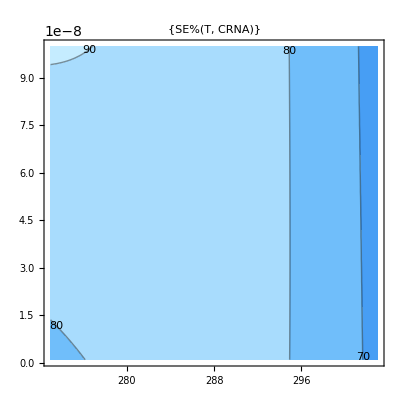

```mathematica
p1=ContourPlot[holo[T,r,1.5*10^-6]-holo[T,r,0.01*10^-6],{T,273,303},{r,1*10^-9,100*10^-9},Contours->{10,20,30,40,50,60,70,80,90,100},ColorFunction->ColorData["DeepSeaColors"],ContourLabels->True,PlotLabel->{"SE%(T, CRNA)"},PlotRange->{0,100}]
```

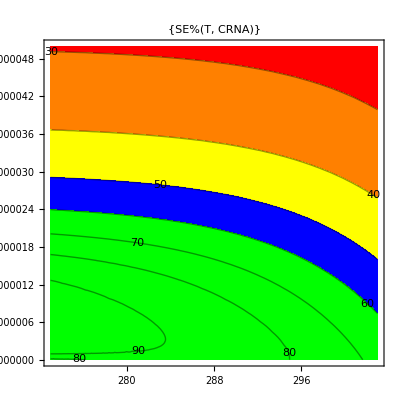

```mathematica
p1=ContourPlot[holo[T,r,1.5*10^-6]-holo[T,r,0.01*10^-6],{T,273,303},{r,1*10^-9,5*10^-6},Contours->{10,20,30,40,50,60,70,80,90,100},ContourShading->{Red,Red,Red,Orange,Yellow,Blue,Green,Green,Green,Green},ContourLabels->True,PlotLabel->{"SE%(T, CRNA)"},PlotRange->{0,100}]
```

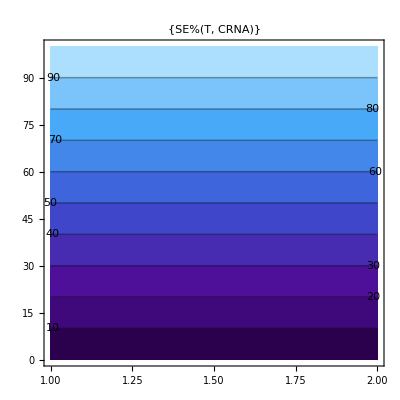

```mathematica
schoen[x_,y_]:=(x/x)+y-1
p1=ContourPlot[schoen[x,y],{x,1,2},{y,0,100},Contours->{10,20,30,40,50,60,70,80,90,100},ColorFunction->ColorData["DeepSeaColors"],ContourLabels->True,PlotLabel->{"SE%(T, CRNA)"},PlotRange->{0,100}]
```

```mathematica
150*10^6/(30*60*24*7*4*12)//N
```

10.334